0.7 x+0.5 x^2+0.2 Log[x]+3 x Log[x]+5 Log[x]^2+0.3 Log[1+x]

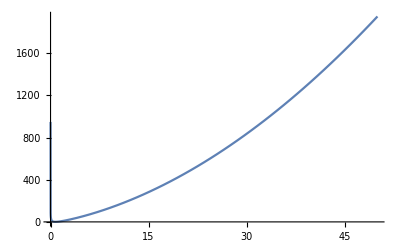

```mathematica
func=a*x+b*x^2+c*Log[x]+d*Log[1+x]+e*(Log[x])^2+f*(x*Log[x]);
subst={a->0.7,b->0.5,c->0.2,d->0.3,e->5,f->3};
testfunc=func/.subst
Plot[testfunc,{x,0,50}]
```

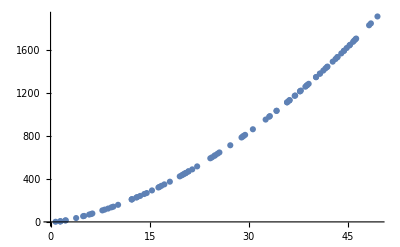

```mathematica
nDatapoint=100;
noise=1;
randomX=Table[RandomReal[{-1,50}],{i,nDatapoint}];
Y=Table[testfunc/.x->randomX[[i]],{i,nDatapoint}];
randomY=Table[Y[[i]]+RandomReal[{-noise,noise}],{i,nDatapoint}];
XY=Thread[{randomX,randomY}];
ListPlot[XY]
```

```mathematica
ClearAll["basisvector"]
ClearAll["curve0"]
ClearAll["w"]
ClearAll["errorfunc"]
```

```mathematica
basisvector[x_]={1,x,x^2,Log[x],Log[1+x], (Log[x])^2,x*Log[x]};
curve0[x_]=Transpose[w].basisvector[x];
η=10^-11(*Learning rate*);
```

```mathematica
ϕ2=Table[basisvector[randomX[[j]]][[k]],{j,1,nDatapoint},{k,1,Length[basisvector[1]]}];(*Design matrix*)
ϕ2//MatrixForm;
ϕ1=Rationalize[ϕ2,10^-20];
invϕ=Inverse[Transpose[ϕ1].ϕ1].Transpose[ϕ1];
SingularValueDecomposition[ϕ1];
N@invϕ.ϕ2//MatrixForm;
```

$Aborted

```mathematica
N[Out[1969]]
```

General::munfl: 1.11903 8.11798727531347×10^-778 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -9.4657×10^-63 8.11798727531347×10^-778 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.0224901 8.11798727531347×10^-778 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{{{0.358245,0.3585,0.350169,0.341744,0.342313,0.080115,-0.31051,0.,0.,0.},{0.376077,0.376034,0.374202,0.369827,0.367829,0.128078,-0.308594,0.,0.,0.},{0.146153,0.149001,0.0839049,0.0520149,0.103735,-0.364734,-0.328382,0.,.`,0.},{0.374881,0.374858,0.372584,0.367931,0.366095,0.124814,-0.308724,0.562,0.610989952836401,0.295526649375074},{0.378715,0.378628,0.377771,0.374012,0.371661,0.135296,-0.308305,0.,0.,0.391948057889531},{0.416425,0.415678,0.42917,0.434617,0.42799;3,0.241811,-0.30404,0.,0.,0.},{0.471132,0.469376,0.504846,0.524825,0.514512,0.406901,-0.297398,0.,0.,0.},{0.0643912,0.0672045,0.00253734,-0.00821333,0.0542594,-0.466897,-0.332473,0.,0.,0.00158869},{0.0260325,0.0281203,-0.0208652,-0.00150109,0.033276,-0.497156,-0.333689,0.,1.50884×10^-7,0.},{0.157182,0.159962,0.0963716,0.0638151,0.112488,-0.347943,-0.327693,5.84344×10^-7,0.,0.}},{{4342.64,0.,0.,0.,0.,0.,0.},{0.,49.033,0.,0.,0.,0.,0.},{0.,0.,3.91071,0.,0.,0.,0.},{0.,0.,0.,0.470664,0.,0.,0.},{0.,0.,0.,0.,0.0296828,0.,0.},{0.,0.,0.,0.,0.,0.000588891,0.},{0.,0.,0.,0.,0.,0.,4.03604×10^-6},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.},{0.961317,0.889689,0.430899,0.0784768,0.141756,0.11423,0.00842392}}}

```mathematica
weight=invϕ.randomY;
```

```mathematica
curve2[x]=Transpose[weight].basisvector[x]
curve=curve2[x];
Y2=Table[curve/.x->randomX[[i]],{i,nDatapoint}];
randomY2=Table[Y2[[i]],{i,nDatapoint}];
```

-7.45058×10^-9+0.7 x+0.5 x^2+0.2 Log[x]+3. x Log[x]+5. Log[x]^2+0.3 Log[1+x]

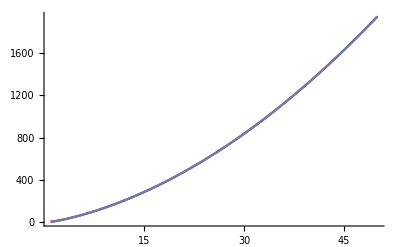

```mathematica
p1=Plot[curve,{x,1,50},PlotStyle->Red];
p2=Plot[testfunc,{x,1,50}];
Show[p1,p2]
```

```mathematica
iternation=30;
trainingset=Table[randomX[[j]]->randomY2[[j]],{j,iternation}];
testset=Table[randomX[[nDatapoint-j]]->randomY2[[nDatapoint-j]],{j,(nDatapoint-iternation)}];
```

Part::partw: Part 11 of {38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246} does not exist.

Part::partw: Part 11 of {1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971} does not exist.

Part::partw: Part 12 of {38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
p=Predict[trainingset];
PredictorMeasurements[p,testset]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value ({1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦11⟧).

PredictorMeasurements::wrgfunc: The first argument should be a predictor, a list of predictions, or a list of distributions instead of Predict[{38.2897→1246.84,39.8102→1330.,18.9336→404.273,39.7085→1324.37,40.0341→1342.46,43.2092→1524.75,47.7367→1803.08,10.2404→159.319,5.42821→61.2839,20.0246→440.971,«20»}].

PredictorMeasurements[Predict[{38.2897→1246.84,39.8102→1330.,18.9336→404.273,39.7085→1324.37,40.0341→1342.46,43.2092→1524.75,47.7367→1803.08,10.2404→159.319,5.42821→61.2839,20.0246→440.971,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦11⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦11⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦12⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦12⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦13⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦13⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦14⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦14⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦15⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦15⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦16⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦16⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦17⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦17⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦18⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦18⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦19⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦19⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦20⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦20⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦21⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦21⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦22⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦22⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦23⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦23⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦24⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦24⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦25⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦25⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦26⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦26⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦27⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦27⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦28⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦28⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦29⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦29⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦30⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦30⟧}],{}]

```mathematica
b=30
testfunc/.x->b
p[b]
```

30

836.659

Predict[{38.2897→1246.84,39.8102→1330.,18.9336→404.273,39.7085→1324.37,40.0341→1342.46,43.2092→1524.75,47.7367→1803.08,10.2404→159.319,5.42821→61.2839,20.0246→440.971,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦11⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦11⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦12⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦12⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦13⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦13⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦14⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦14⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦15⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦15⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦16⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦16⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦17⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦17⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦18⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦18⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦19⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦19⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦20⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦20⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦21⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦21⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦22⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦22⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦23⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦23⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦24⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦24⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦25⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦25⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦26⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦26⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦27⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦27⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦28⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦28⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦29⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦29⟧,{38.2897,39.8102,18.9336,39.7085,40.0341,43.2092,47.7367,10.2404,5.42821,20.0246}⟦30⟧→{1246.84,1330.,404.273,1324.37,1342.46,1524.75,1803.08,159.319,61.2839,440.971}⟦30⟧}][30]